```mathematica
str="EUR
EUR
EUR
EUR
EUR
EUR
EUR
EUR
EUR
EUR
EUR
EUR
EUR
EUR
EUR
GTQ
GTQ
MAD
MAD
MAD
MAD
KRW
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
USD
USD
USD
USD
USD
USD
USD
USD
USD
USD
USD
USD
USD
USD
USD
USD
USD
VND
VND";
```

```mathematica
curr=Union[StringSplit[str]]
```

{EUR,GBP,GTQ,KRW,MAD,USD,VND}

```mathematica
conversions= AssociationMap[QuantityMagnitude[CurrencyConvert[Quantity[1,#],"EUR"]]&,curr]
```

<|EUR→1,GBP→1.10583,GTQ→0.108524,KRW→0.000750413,MAD→0.0921225,USD→0.84246,VND→0.0000363882|>

```mathematica
Export["/Users/katjad/Documents/Github/CS146/LBA/conversions.json",conversions]
```

/Users/katjad/Documents/Github/CS146/LBA/conversions.json

```mathematica
conversions["KRW"]
```

0.000750413

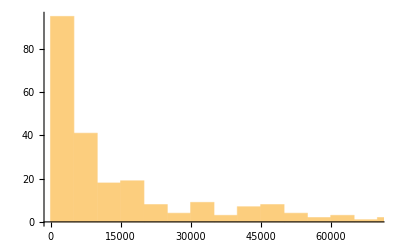

```mathematica
Histogram[Divide@@@DeleteMissing[EntityValue["Country",{"GDP","Population"}],1,2],{5000},PlotRange->{{0,70000},All}]
```

```mathematica
EntityValue[{Entity["Country","Germany"],Entity["Country","UnitedKingdom"],Entity["Country","UnitedStates"],Entity["Country","SouthKorea"],Entity["Country","Morocco"],Entity["Country","Vietnam"],Entity["Country","Guatemala"]},]
```

```mathematica
Divide@@@DeleteMissing[EntityValue[{Entity["Country","Germany"],Entity["Country","UnitedKingdom"],Entity["Country","UnitedStates"],Entity["Country","SouthKorea"],Entity["Country","Morocco"],Entity["Country","Vietnam"],Entity["Country","Guatemala"]},{"GDP","Population"},"EntityAssociation"],1,2]
```

<|Germany→46046. $,United Kingdom→41864.5 $,United States→65116.9 $,South Korea→32061.9 $,Morocco→3255.27 $,Vietnam→2715.28 $,Guatemala→4363.14 $|>